```mathematica
3*4
```

12

```mathematica
5/3
```

5/3

```mathematica
N[5/3]
```

1.66667

```mathematica
N[5/3,100]
```

1.666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
5.0/3
```

1.66667

```mathematica
((2.4+3.56)*4.8)^3/(2.6+1.8)
```

5321.2

```mathematica
Hold[((2.4+3.56)*4.8)^3/(2.6+1.8)]
```

Hold[((2.4+3.56) 4.8)^3/(2.6+1.8)]

```mathematica
x * y
```

x y

```mathematica
((x+y)*z)^3/(x+y)
```

(x+y)^2 z^3

```mathematica
Hold[((x+y)*z)^3/(x+y)]
```

Hold[((x+y) z)^3/(x+y)]

```mathematica
Sin[x]^2 + Cos[x]^2
```

Cos[x]^2+Sin[x]^2

```mathematica
Simplify[Sin[x]^2 + Cos[x]^2]
```

1

```mathematica
Simplify[Sqrt[x^2]]
```

√(x^2)

```mathematica
Simplify[Sqrt[x^2],x < 0]
```

-x

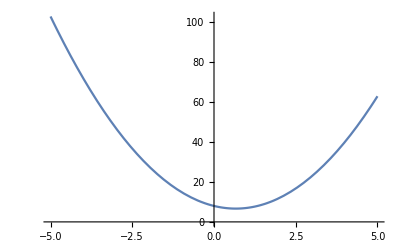

```mathematica
Plot[3.*x^2-4.*x+8.,{x, -5,5}]
```

```mathematica
term1 = 3. *x^2 -4.*x + 8
```

8-4. x+3. x^2

```mathematica
term1
```

8-4. x+3. x^2

```mathematica
x = 3.
```

3.

```mathematica
term1
```

23.

```mathematica
Clear[x]
```

```mathematica
term1
```

8-4. x+3. x^2

```mathematica
term2 = D[term1,x]
```

-4.+6. x

```mathematica
term3 = Integrate[term1,x]
```

8 x-2. x^2+1. x^3

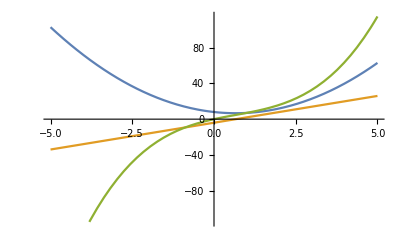

```mathematica
Plot[{term1,term2,term3},{x,-5,5}]
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

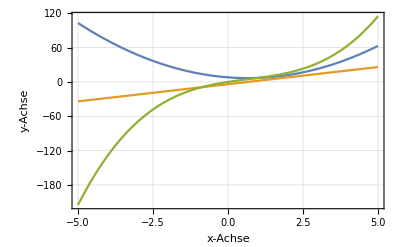

```mathematica
Plot[{term1,term2,term3},{x,-5,5},Frame -> True, GridLines -> Automatic, FrameLabel-> {"x-Achse","y-Achse"},PlotRange -> All]
```

```mathematica
va = {1,2,3}
```

{1,2,3}

```mathematica
vb = {a,b,c}
```

{a,b,c}

```mathematica
va + vb
```

{1+a,2+b,3+c}

```mathematica
3*vb
```

{3 a,3 b,3 c}

```mathematica
va * vb
```

{a,2 b,3 c}

```mathematica
va . vb
```

a+2 b+3 c

```mathematica
Cross[va,vb]
```

{-3 b+2 c,3 a-c,-2 a+b}

```mathematica
FullForm[vb]
```

List[a,b,c]

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
Apply[Plus,vb]
```

a+b+c

```mathematica
Apply[Plus,va]
```

6

```mathematica
mat = {{a,b,c},{d,e,f}}
```

{{a,b,c},{d,e,f}}

```mathematica
MatrixForm[mat]
```

(a | b | c
d | e | f)

```mathematica
mat . va
```

{a+2 b+3 c,d+2 e+3 f}

```mathematica
va . mat
```

Dot::dotsh: Tensors {1,2,3} and {{a,b,c},{d,e,f}} have incompatible shapes.

{1,2,3}.{{a,b,c},{d,e,f}}

```mathematica
FullForm[mat]
```

List[List[a,b,c],List[d,e,f]]

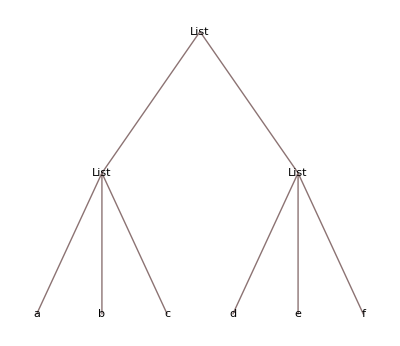

```mathematica
TreeForm[mat]
```

```mathematica
Apply[Plus,mat]
```

{a+d,b+e,c+f}

```mathematica
Apply[Plus,mat,{1}]
```

{a+b+c,d+e+f}

```mathematica
mat[[2]]
```

{d,e,f}

```mathematica
mat[[2,1]]
```

d

```mathematica
mat[[All,2]]
```

{b,e}

```mathematica
?;;
```

i;;j represents a span of elements i through j.
i;; represents a span from i to the end.
;;j represents a span from the beginning to j.
;; represents a span that includes all elements.
i;;j;;k represents a span from i through j in steps of k.
i;;;;k represents a span from i to the end in steps of k.
;;j;;k represents a span from the beginning to j in steps of k.
;;;;k represents a span from the beginning to the end in steps of k.

```mathematica
mat[[1;;-1,2]]
```

{b,e}

```mathematica
mat[[1;;2,2;;3]]
```

{{b,c},{e,f}}

```mathematica
Det[mat[[1;;2,2;;3]]]
```

-c e+b f